```mathematica
V[r_,M_,R_]=Assuming[x>=0&&M>=0&&R>=0&&r∈Reals&&M∈Reals&&R∈Reals,{Integrate[1/(√(1-2 M x^2/R^3))x^2,{x,0,r}]}]
```

{ConditionalExpression[(-2 r √(M (-2 M r^2+R^3))+√2 R^3 ArcSin[√2 r √(M/R^3)])/(8 (M/R)^(3/2)),r≥0&&(2 M r^2<R^3||r≤0||R≤0)]}

```mathematica
(*V[r_,M_,R_]=Integrate[1/(√(1-2 M x^2/R^3))x^2,{x,0,r},Assumptions->M∈Reals,Assumptions->r∈Reals,Assumptions->R∈Reals,Assumptions->M>=0,Assumptions->R≥0]*)
```

```mathematica
tV[M_,R_]=V[R,M,R]
```

{ConditionalExpression[(-2 R √(M (-2 M R^2+R^3))+√2 R^3 ArcSin[√2 √(M/R^3) R])/(8 (M/R)^(3/2)),R≥0&&(2 M R^2<R^3||R≤0||R≤0)]}

```mathematica
Clear[tρ]
tρ[M_,R_]=M/tV[M,R]
tρ[M,1]
tρ[1,R]
```

{ConditionalExpression[(8 M (M/R)^(3/2))/(-2 R √(M (-2 M R^2+R^3))+√2 R^3 ArcSin[√2 √(M/R^3) R]),R≥0&&(2 M R^2<R^3||R≤0||R≤0)]}

{ConditionalExpression[(8 M^(5/2))/(-2 √((1-2 M) M)+√2 ArcSin[√2 √M]),M<1/2]}

{ConditionalExpression[(8 (1/R)^(3/2))/(-2 R √(-2 R^2+R^3)+√2 R^3 ArcSin[√2 √(1/R^3) R]),R==0||(R≥0&&-2 R^2+R^3>0)]}

This calculation should only be valid before the dust form a black hole.

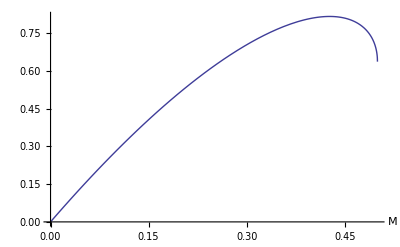

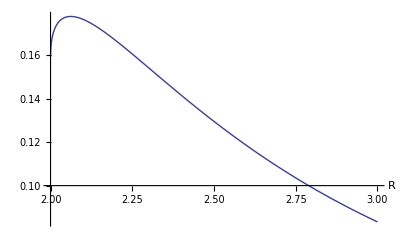

```mathematica
Plot[tρ[M,1],{M,0,0.5},AxesLabel->Automatic]
Plot[tρ[1,R],{R,2,3},AxesLabel->Automatic]
```

```mathematica
tρM1[M_]=D[tρ[M,1],M]
tρM1[0.5]
maxfixR=MaxValue[(8 M^(5/2))/(-2 √((1-2 M) M)+√2 ArcSin[√2 √M]),M]
N[maxfixR]
tρR1[R_]=D[tρ[1,R],R]
tρR[2]
maxfixM=MaxValue[(8 (1/R)^(3/2))/(-2 R √(-2 R^2+R^3)+√2 R^3 ArcSin[√2 √(1/R^3) R]),R]
N[maxfixM]
```

{ConditionalExpression[-(8 M^(5/2) (1/(√(1-2 M) √M)-(1-4 M)/(√((1-2 M) M))))/(-2 √((1-2 M) M)+√2 ArcSin[√2 √M])^2+(20 M^(3/2))/(-2 √((1-2 M) M)+√2 ArcSin[√2 √M]),M<1/2]}

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

{Undefined}

$Aborted

0.

{ConditionalExpression[-(8 (1/R)^(3/2) ((√2 (-(3 √(1/R^3))/(√2)+√2 √(1/R^3)) R^3)/(√(1-2/R))-(R (-4 R+3 R^2))/(√(-2 R^2+R^3))-2 √(-2 R^2+R^3)+3 √2 R^2 ArcSin[√2 √(1/R^3) R]))/((-2 R √(-2 R^2+R^3)+√2 R^3 ArcSin[√2 √(1/R^3) R])^2)-(12 (1/R)^(5/2))/(-2 R √(-2 R^2+R^3)+√2 R^3 ArcSin[√2 √(1/R^3) R]),R==0||(R≥0&&-2 R^2+R^3>0)]}

tρR[2]

$Aborted

$Aborted

```mathematica
Plot3D[{tρ[M,R]},{M,0,1},{R,0,3},Mesh->All,AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

## Draft

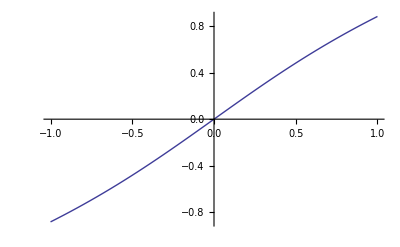

```mathematica
Plot[ArcSin[θi],{θi,-1,1}]
```